```mathematica
initialize[]:=Module[{timg, im, tim},(
SetDirectory[NotebookDirectory[]];
timg = -Graphics-;
(*timg =Image@Import["Analysis/2D/circles/no_nu.png"];
timg =ColorNegate@Image@Import["Analysis/2D/angdist/no_u.png"];*)
tim=ImageResize[getBinarizedImage[timg, 1, 3, 0.1], {100,100}];
Print@Show[tim];
img=tim;
)];
perform[]:=Module[{nR, nC, graphic1, graphic2, graphic3, vectField1, vectField2, vectField3, vectFields1, vectFields2, vectField4, oriPlot1, oriPlot2, oriPlot3, oriPlot4, oriWeights, oriWeightsF, iow,error, f1, f2, f3, f4, f5, f6, f7, f8, f9, lvp1, lvp2, lvp3, in, pointsToShow, time1, time2, time3, time4, time5, angleRes, caseNumber},(
time1=TimeUsed[];
{nR, nC}=ImageDimensions@img;
vectFields1={};
vectFields2={};
If[nR>100, pointsToShow=100, pointsToShow=All];
angleRes =0.25;
caseNumber =2;
in=Graphics@Inset[img,{0,0},{-0.5,-0.5}, img//ImageDimensions];

Print["Weighted Vector Summation Algorithm"];
vectFields1= vectorSummation2D[img, #] &/@ {5};
vectField1 =normalizedVectorField2DMean[vectFields1];
lvp1=Graphics@ListVectorPlot[vectField1//Reverse//Transpose,PlotTheme->"Scientific",VectorScale->Small, VectorPoints->pointsToShow];
graphic1 =Show[{in, lvp1},ImageSize->Large,Axes->True, PlotRange->{{0,nR},{0,nC}}];
Print@graphic1;
vf1=vectField1;
vfs1 = vectFields1;
Do[(
ivf1=interpolationVectorField2D[vectFields1[[i]], img];
{oriWeights, oriPlot1}=vecFieldToAngleDistribution2D[ivf1, False,angleRes];
error=calculateAbsoluteError[oriWeights, idealOriWeights[caseNumber,angleRes,img]];
Print["Error weighted vector summation, one of the windows : ", error];
),{i,1,vectFields1//Length}];
ivf1=interpolationVectorField2D[vectField1, img];
{oriWeights, oriPlot1}=vecFieldToAngleDistribution2D[ivf1, False,angleRes];
Print@oriPlot1;
error=calculateAbsoluteError[oriWeights, idealOriWeights[caseNumber,angleRes,img]];
Print["Error weighted vector summation, Final : ", error];
time2 = TimeUsed[];

Print["Moment of Inertia Algorithm"];
vectFields2=momentOfInertia2D[img, 1#] &/@ {3,5,7,9,11,17};
vectField2 =normalizedVectorField2DMean[vectFields2];
lvp2=Graphics@ListVectorPlot[vectField2//Reverse//Transpose,PlotTheme->"Scientific",VectorScale->0.02, VectorPoints->pointsToShow];
graphic2 =Show[{in, lvp2},ImageSize->Large,Axes->True, PlotRange->{{0,nR},{0,nC}}];
Print@graphic2;
vf2=vectField2;
vfs2 = vectFields2;
Do[(
{oriWeights, oriPlot1}=vecFieldToAngleDistribution2D[vectFields2[[i]], False,angleRes];
error=calculateAbsoluteError[oriWeights, idealOriWeights[caseNumber,angleRes,img]];
Print["Error Moment of Inertia, one of the ROIs : ", error];
),{i,1,vectFields2//Length}];
{oriWeights, oriPlot2}=vecFieldToAngleDistribution2D[vf2, False, angleRes];
Print@oriPlot2;
error=calculateAbsoluteError[oriWeights, idealOriWeights[caseNumber,angleRes,img]];
Print["Error Moment of Inertia, overall : ", error];
time3 = TimeUsed[];

Print["Fourier Transformation Algorithm"];
{f1, f2, f3, f4, f5, f6, f7, f8, f9, oriWeightsF}=fourierDo[img, 2];
Print[f1, f2, f3, f4, f5, f6, f7, f8, f9];
iow =idealOriWeights[caseNumber,0.25,img];
error=calculateAbsoluteError[standardizeList[oriWeightsF, iow], iow];
Print["Error Fourier Analysis Method : ", error];
time4 = TimeUsed[];

Print["Gradient Filter Algorithm"];
vectField3 =findOrientationGradFilter[img];
vectField4=interpolationVectorField2D[vectField3, img];
lvp3=Graphics@ListVectorPlot[vectField3//Reverse//Transpose,PlotTheme->"Scientific",VectorScale->0.05, VectorPoints->pointsToShow];
graphic3 =Show[{in, lvp3},ImageSize->Large,Axes->True, PlotRange->{{0,nR},{0,nC}}];
Print@graphic3;
vf3=vectField3;
ivf3=vectField4;
{oriWeights, oriPlot3}=vecFieldToAngleDistribution2D[ivf3, False, angleRes];
Print@oriPlot3;
error=calculateAbsoluteError[oriWeights, idealOriWeights[caseNumber,angleRes,img]];
Print["Error Graphic Orientation Filter Method : ", error];
time5 = TimeUsed[];

vf=normalizedVectorField2DMean[{ivf1,vf2,ivf3}];
Print["Time taken for Vector Summation: ", time2-time1, " (s)"];
Print["Time taken for Moment of Inertia: ", time3-time2, " (s)"];
Print["Time taken for Fourier Analysis: ", time4-time3, " (s)"];
Print["Time taken for Gradient Filter: ", time5-time4, " (s)"];
Print["Total time consumed was: ", TimeUsed[]-time1, " (s)"];
)];


(*************** MISCELLANEOUS HELPER FUNCTIONS *************)

generateVectorField[r_, c_, d_, layers_:1]:=Module[{vecField, vecPlot},(
If[layers===1, (vecField=RandomReal[{-1,1}, {r, c, d}];)];
If[layers>1, (vecField=RandomReal[{-0.5,1}, {layers,r, c, d}];)];
If[d===2,vecPlot=ListVectorPlot[vecField];];
If[d===3,vecPlot=ListVectorPlot3D[vecField];];
Return[{vecField,vecPlot}];
)];
vecFieldToAngleDistribution2D[vecField_, weighted_:False, resolution_:0.1]:=Module[{oriWeights, oriPlot, nR, nC, nD, theta, rounded,  v, weight, fitCurve, fitPlot, dataPlot},(
{nR, nC, nD}=vecField//Dimensions;
oriWeights=ConstantArray[0, {Round[180*resolution],2}];
(oriWeights[[#, 1]]=Round[#/resolution])&/@Range[Round[180*resolution]];
Do[(
v =N@vecField[[r, c]];
If[!(v[[1]]==0 && v[[2]]==0), (
theta = ArcTan[v[[1]], v[[2]]]/Degree;
(*If[theta<0,theta=180-theta];*)
rounded =Round[theta*resolution]/resolution;
(*Print["Theta: ",theta, " , Rounded: ",rounded];*)
If[rounded==0, rounded=180];
weight = Norm[v];
If[weighted,(
oriWeights[[Round[rounded*resolution], 2]]+=weight;
),(
oriWeights[[Round[rounded*resolution], 2]]+=1;
)];
)];
),{r, 1, nR}, {c, 1, nC}];

fitCurve=Fit[oriWeights,{1,x,x^2,x^3, x^4, x^5, x^6,x^7, x^8},x];
(*angularAmplitudePlot = Labeled[,Style["Angular Amplitude Plot", 18]];*)

fitPlot = Plot[fitCurve, {x,0,180}];
dataPlot =ListPlot[oriWeights];
oriPlot = Labeled[Show[(*fitPlot,*) dataPlot, PlotRange-> {{0, 180},{0,Automatic}} ,Axes->{False, True}, ImageSize->450,FrameLabel->{"Orientation (deg)","Amplitude"}, Frame->True],Style["Orientation distribution", 18]];
Return[{oriWeights,oriPlot}];
)];

calculateAbsoluteError[oriWeight1_, oriWeight2_]:=Module[{p1s, p2s, angle,  freq1, freq2, sum,count,averageAbsoluteError},(
p1s={};
p2s={};
sum=0;
Do[(
{angle,freq1} = oriWeight1[[i]];
{angle,freq2} = oriWeight2[[i]];
If[freq1>0,(p1s=Join[p1s,ConstantArray[angle,freq1]];)];
If[freq2>0, p2s=Join[p2s,ConstantArray[angle,freq2]];];
),{i,1,Length@oriWeight1}];
Print["Lengths of p1s and p2s: ",{Length@p1s, Length@p2s}];
count=Min[{Length@p1s, Length@p2s}];
Do[(
sum+=Abs[p1s[[i]]-p2s[[i]]];
),{i, 1, count}];
averageAbsoluteError=N@(sum/count);
Return[averageAbsoluteError];
)];

standardizeList[listToChange_, standardList_]:=Module[{res,l, standardNorm, currentNorm},(
standardNorm =Norm[standardList[[All,2]],1];
currentNorm =Norm[listToChange[[All,2]],1];
l=Round[N[listToChange[[All,2]]*(standardNorm/currentNorm)]];
res =Transpose[{listToChange[[All,1]],l[[All]]}];
Return@res;
)];
idealOriWeights[case_:1, resolution_:0.1, img_]:=Module[{oriWeights,imd,mass, angle1Pos, angle2Pos, t},(
imd=Transpose@ImageData[img];
mass=Total[Flatten[imd]];
oriWeights=ConstantArray[0, {Round[180*resolution],2}];
(oriWeights[[#, 1]]=Round[#/resolution])&/@Range[Round[180*resolution]];
If[case==1,(
oriWeights[[Round[90*resolution], 2]]+=mass;
)];
If[case==2,(
oriWeights[[All,2]]=ConstantArray[Round[mass/Length@oriWeights], Length@oriWeights];
)];
If[case==3,(
angle1Pos =Round[45*resolution];
angle2Pos =Round[135*resolution];
t =Round[2*mass/Length@oriWeights];
oriWeights[[1;;angle1Pos,2]]=ConstantArray[t, angle1Pos];
oriWeights[[angle2Pos;;Length@oriWeights,2]]=ConstantArray[t, angle1Pos+1];
(*Print["angle1Pos = ", angle1Pos];
Print["angle2Pos = ", angle2Pos];
Print["t = ", t];
Print["oriweights = ",oriWeights];*)
)];
Return[oriWeights];
)];

meanFilterVectorField2D[vecField_, radius_:1]:=Module[{sum,count,nRows,nCols,nDim,res,vx,vy,isZero},(
{nRows, nCols, nDim}=vecField//Dimensions;
res=vecField;
Do[(
{vx,vy}=vecField[[r,c]];
isZero =!(Abs@vx>0.0001 || Abs@vy>0.0001 );
If[!isZero,(
sum={0,0,0};
count=0;
Do[(
{vx,vy}=vecField[[l,m]];
If[Abs@vx>0.0001 || Abs@vy>0.0001, (
sum+={vx,vy};
count++;
)];
),{l,r-radius,r+radius},{m,c-radius,c+radius}];
If[count>1 ,(
res[[r,c]]=N[sum/count];
)];
)];
),{r, 1+radius,nRows-radius},{c, 1+radius, nCols-radius}];
Return[res];
)];

meanVectorFields2D[vecs_]:=Module[{total, mean },(
total=Sum[vecs[[i]],{i,Length@vecs}];
mean = N[total/(Length@vecs)];
Return[mean];
)];

normalizedVectorField2DMean[vecFields_]:=Module[{vecField, norms, norm,averageNorm, normalizedVecFields, normalizedVecField, res},(
norms={};
normalizedVecFields={};
Do[(
norm=Norm[Flatten[vecFields[[i]],2]];
AppendTo[norms, norm];
),{i, vecFields//Length}];
averageNorm = Mean[norms];
Do[(
normalizedVecField=vecFields[[i]]*(averageNorm/norms[[i]]);
AppendTo[normalizedVecFields, normalizedVecField];
),{i, vecFields//Length}];
res = meanVectorFields2D[normalizedVecFields];
Return@res;
)];

interpolationVectorField2D[vecField_, img_]:=Module[{nRows,nCols, nDim, coordsOfNonZeroPoints, res,vx,vy, i,imgdata,  nearestR, nearestC},(
{nRows,nCols, nDim}=vecField//Dimensions;
imgdata = ImageData@img;
coordsOfNonZeroPoints ={};
res=vecField;
Do[(
{vx,vy}=vecField[[r,c]];
If[(Abs@vx>0.05 || Abs@vy>0.05 ),(
AppendTo[coordsOfNonZeroPoints, {r,c}];
)];
),{r, 1,nRows},{c, 1, nCols}];

Do[(
i=imgdata[[r,c]];
If[i>0.2 ,(
{ nearestR, nearestC} = Nearest[coordsOfNonZeroPoints, {r,c}][[1]];
res[[r,c]]=vecField[[nearestR, nearestC]];
),(
res[[r,c]]={0,0};
)];
),{r, 1,nRows},{c, 1, nCols}];
Return[res];
)];

saveVectorFieldInFile[vectorField_]:=Module[{},
Export["vect.dat",vectorField];
];

(*************** SEGMENTATION BINARIZATION FUNCTIONS *************)

firstPrincipalComponentFromRGB[img_]:=Module[{pcs, pc},(
pcs =(KarhunenLoeveDecomposition[ColorSeparate[img]])[[1]];
pc=pcs[[1]];
Return[pc];
)];

getBinarizedImage[im_, method_:1, radius_:3, threshold_:0.4]:=Module[{meanFiltered, gradientFiltered, isrgb, img, binarized, sobelX, sobelY, sobelIm},(
binarized=Null;
img=im;
If[img//ImageData//Dimensions//Length >2, (isrgb=True), (isrgb =False)];
If[isrgb,(
img =firstPrincipalComponentFromRGB[im];
),(
img=RemoveAlphaChannel@ColorConvert[im,"Grayscale"];
)];
meanFiltered =MeanFilter[img,radius];
If[method== 1, (
binarized=Binarize[img];
)];
If[method== 2, (
binarized=MorphologicalBinarize[img,FindThreshold[img, Method->"Cluster"]];
)];
If[method== 3, (
gradientFiltered =GradientFilter[img,radius]//ImageAdjust;
binarized =getBinarizedImage[gradientFiltered, 1];
)];
If[method== 4, (
sobelY={{1,2,1},{0,0,0},{-1,-2,-1}}/4.;sobelX={{1,0,-1},{2,0,-2},{1,0,-1}}/4.;
sobelIm =Image[Sqrt[ImageData[ImageConvolve[meanFiltered, sobelX]]^2 + ImageData[ImageConvolve[meanFiltered, sobelY]]^2]]//ImageAdjust;
binarized =MorphologicalBinarize[sobelIm];
)];
If[method== 5, (
binarized =EdgeDetect[GaussianFilter[img, radius], Method->"Sobel"];
)];
If[method== 6, (
binarized =MorphologicalBinarize[meanFiltered, {threshold,FindThreshold[meanFiltered]}]
)];
Return[binarized];
)];

(*************** WEIGHTED VECTOR SUMMATION 2D *************)

graphVectors[vecs_]:=Module[{graf},(
graf =Graphics[Arrow[{{0, 0}, #}]&/@vecs,Axes->True];
Return[graf];
)];
vectorSummation2D[image_, window_]:=Module[{img, imgdata, nRows, nCols, vectors, tv, center, lengths, l, weighted1Vectors, images, vec, img1, img2, vari, meanIntensity, w2, pixelValues, pixValues, runningTotalX, runningTotalY, weightedVector, axialWV,vectorField, tempv,temp, timeStart, timeEnd},(
timeStart = TimeUsed[];
img=ColorConvert[image,"GrayScale"];
imgdata = ImageData@img;
{nRows, nCols} = ImageDimensions[img];
vectors = {};
weighted1Vectors = {};
lengths = {};
center =Ceiling[window/2];
Do[(
If[!(i>=center && j===center), (
tv={(i-center), (center-j)};
AppendTo[vectors, tv];
l = Sqrt[tv[[1]]^2 + tv[[2]]^2];
AppendTo[lengths,l];
AppendTo[weighted1Vectors, tv/(l^2)];
)];
), {i, 1, window}, {j, 1, center}];

runningTotalX = ConstantArray[0,{nRows, nCols}];
runningTotalY = ConstantArray[0,{nRows, nCols}];

(*Print[graphVectors[Join[weighted1Vectors, -weighted1Vectors]]];*)

Do[(
vec = vectors[[i]];
l = lengths[[i]];
img1 =ImageTransformation[img,#+{vec[[1]]/nCols, vec[[2]]/nRows}&];
img2 =ImageTransformation[img,#+{-vec[[1]]/nCols, -vec[[2]]/nRows}&];
images={img1, img, img2};
(*Print["Vector: ", vec];
Print[images];*)

Do[(
If[imgdata[[r,c]]>0.5,(
pixValues = {};
(*Print["r, c : ",{r, c}];*)
pixValues=(ImageData[#])[[r, c]]&/@ images;
(*Print["pixvalues: ", pixValues];*)
If[True||Variance[pixValues]!=0, (
meanIntensity = Mean[pixValues];
vari =Variance[pixValues];
(*Print["vari: ", vari];*)
w2 =Sqrt[1/3]-Sqrt[vari];
weightedVector=(vec/(l))*w2;
(*Print["weighted vector: ",  weightedVector];*)
axialWV =vectorAngleMultiply[weightedVector, 2];
runningTotalX[[r, c]] += axialWV[[1]];
runningTotalY[[r, c]] += axialWV[[2]];
)];
)];
(*),{r,20,25}, {c, 51, 52}];*)
),{r,center,nRows-center}, {c, center, nCols-center}];
),{i, 1, Length[vectors]}];

vectorField =ConstantArray[{0,0},{nRows, nCols}];
Do[(
If[imgdata[[r,c]]>0.5,
tempv ={runningTotalX[[r,c]], runningTotalY[[r,c]]};
temp = vectorAngleMultiply[tempv,0.5];
If[temp[[2]]<0, tempv=-temp;, tempv=temp];
vectorField[[r, c]]=tempv;
];

(*Print["vector at ", {r, c}, " is : ", vectorField[[r,c]]];
Print["image at ", {r, c}, " is : ", imgdata[[r,c]]];*)
),{r,center,nRows-center}, {c, center, nCols-center}];
(*),{r,15,25}, {c, 45, 55}];*)
timeEnd = TimeUsed[];
Print["Vector Summation one pass with window=",window," and image size {rows, columns}=", {nRows, nCols}," took ", timeEnd-timeStart, " (s)"];
Return[vectorField];
)];

vectorAngleMultiply[vec_, factor_]:=Module[{theta, mag, res},(
theta=ArcTan[vec[[1]],vec[[2]]];
mag=Norm[vec];
res = Norm[vec]*{Cos[factor theta], Sin[factor theta]};
Return[N@res];
)];
(*************** MOMENT OF INERTIA 2D *************)

drawGraph[img_, nx_,ny_,centroids_,vecs_]:=Module[{results, gra},
results={};

If[Length@centroids[[1]]==0,
(
gra=Graphics[{Inset[img,{0,0},{0,0}, {nx, ny}],Red,Point[centroids],Yellow,Line[{{centroids,(nx/3) vecs+centroids}}]},PlotRange->{{0,nx},{0,ny}}, Axes->True];
Return[gra];
),
(
(*Print["Need to implement drawGraph Else properly ",centroids[[1]]];*)
Do[(
gra=Graphics[{Inset[img,{0,0},{0,0}, {nx, ny}],Red,Point[centroids[[i]]],Yellow,Line[{{centroids[[i]],(nx/3) vecs[[i]]+centroids[[i]]}}]},PlotRange->{{0,nx},{0,ny}}, Axes->True];
AppendTo[results, gra];
),
{i, Length@centroids}
];
Return[gra];
(*Return[Graphics[results, PlotRange->{{0,nx},{0,ny}}, Axes->True]];*)
)];
];

resetVectorField[img_]:=Module [{vectorField, nRows, nCols},
vectorField =img//ImageData;
{nRows, nCols}=img//ImageDimensions;
Do[
If[vectorField[[i,j]]==0, vectorField[[i, j]]={0,0}, vectorField[[i, j]]={1,1}];
,{i, 1, nRows}, {j, 1, nCols}
];
Return[vectorField];
];

findSym[img_]:=Module[{imd,nx,ny,points,weights,mass,com,centroid, centroids, ori, oris, count, vec, vecs, vtemp, lengths, widths, pointsCom,diag,inertia,v1,v2, graf, masks, shapes, subImgs, multiEnabled=True},imd=Transpose@ImageData[RemoveAlphaChannel@ColorConvert[img,"Grayscale"]];
weights=Flatten[imd];
mass=Total[weights];
If[mass==0||mass==1, Return[{0, Null, Null, Null, Null, Null}]];
If[mass==(nx*ny), Return[{0, Null, Null, Null, Null, Null }]];
{nx,ny}=Dimensions[imd];

count =Values[ComponentMeasurements[img, "LabelCount"]][[1]];
If[multiEnabled &&count>1,
(
centroids =Values[ComponentMeasurements[img, "Centroid"]];
oris =Values[ComponentMeasurements[img, "Orientation"]];
lengths = Values[ComponentMeasurements[img, "Length"]];
widths = Values[ComponentMeasurements[img, "Width"]];
masks =Values[ComponentMeasurements[img, "Mask"]];
shapes = Values[ComponentMeasurements[img, "Shape"]];
subImgs =Values[ComponentMeasurements[img, "Image"]];
vecs ={};
Do[(
vtemp =Chop[{Cos[oris[[i]]],Sin[oris[[i]]]}];
AppendTo[vecs, vtemp];
),{i, 1, count}];
(*Print["Centroids_Default = ", centroids];
Print["Vectors = ", vecs];*)
graf=drawGraph[img,nx,ny,centroids, vecs];
Return[{count, vecs, graf, centroids, masks,subImgs}];
)
];
centroid =Values[ComponentMeasurements[img, "Centroid"]][[1]];
ori =Values[ComponentMeasurements[img, "Orientation"]][[1]];
vec =Chop[{Cos[ori],Sin[ori]}];


points=Tuples[{Range[nx],Reverse@Range[ny]}];
com=Total[points weights]/mass//N;
(*Print["Centroid_Custom = ", com];
Print["LabelCount = ", count];
Print["Centroid_Default = ", centroid];
Print["Vector = ", vec];*)

pointsCom=(Subtract[#,com]&/@points) weights;
diag=Total[(#.#)&/@pointsCom];
inertia=Table[KroneckerDelta[i,j] diag-Total[(#[[i]] #[[j]])&/@pointsCom],{i,1,2},{j,1,2}];
{v1,v2}=Eigenvectors[inertia];
graf = drawGraph[Image[Transpose@imd], nx, ny, centroid, vec];
(*graf=Graphics[{Inset[Image[Transpose@imd],{0,0},{0,0}, {nx, ny}],Red,Point[centroid],Yellow,Line[{{centroid,(nx/3) v2+centroid}}]},PlotRange->{{0,nx},{0,ny}}, Axes->True];*)
Return[{count, vec, graf, centroid, Null, Null}];
];

momentOfInertia2D[img_, pixFactor_:10]:=Module[{row1, row2, col1, col2, nRows, nCols, subIm, drows, dcols, count, vec, graf, cen, vectorField, tcol1, tcol2, trow1, trow2, masks, sIs, timeEnd, timeStart},(
timeStart = TimeUsed[];
vectorField = resetVectorField[img];
{nRows, nCols}=img//ImageDimensions;
Do[
row1=Ceiling[(nRows/pixFactor)*(i-1)+1];
row2 = Ceiling[(nRows/pixFactor)*i];
col1=Ceiling[(nCols/pixFactor)*(j-1)+1];
col2 = Ceiling[(nCols/pixFactor)*j];
subIm = ImageTake[
img,{ row1, row2},{ col1, col2 }
];
{drows, dcols}=subIm//ImageDimensions;
{count, vec, graf, cen,masks, sIs}=findSym[subIm];

If[count==1,(
If[!SameQ[vec,Null],(
If[vec[[2]]<0, vec=-vec;];
Do[
If[vectorField[[k,l]]=={1,1},vectorField[[k, l]]=vec];
,{k, row1, row2}, {l, col1, col2}
];
)];
)];

If[count>1, (
Do[(
If[!SameQ[vec[[m]], Null],(
If[vec[[m]][[2]]<0, vec[[m]]=-vec[[m]];];
Do[
If[masks[[m, k-row1+1, l-col1+1]]==1,
vectorField[[k, l]]=vec[[m]];
];
,{k, row1, row2}, {l, col1, col2}
];
),(
Do[
If[masks[[m,  k-row1+1, l-col1+1]]==1,
vectorField[[ k, l]]={0,0};
];
,{k, row1, row2}, {l, col1, col2},
];
)];
),{m,1, count}];
)];

If[count==0, (
Do[
If[vectorField[[k,l]]=={1,1},vectorField[[k, l]]={0,0}];
,{k, row1, row2}, {l, col1, col2}
];
)];
(*Print["Window: Row ", row1, " to ", row2, " , Column ", col1, " to ", col2];
Print["rows=",drows,", cols=" , dcols];
Print["Vector(s) = ", vec];
Print["count = ",count];
Print[graf]*),
(*{i,2, 4}, {j,2, 3}*)
{i,1, pixFactor}, {j,1, pixFactor}
];
(*saveVectorFieldInFile[];*)
timeEnd = TimeUsed[];
Print["Moment of Inertia one pass with iteration factor = ",pixFactor," and image size {rows, columns}=", {nRows, nCols}," took ", timeEnd-timeStart, " (s)"];
Return[vectorField];
)];

(*************** FOURIER TRANFORM METHOD 2D *************)

angularAmplitude[ Po_, theta1_,window_:0.05]:=Module[{pts, sum},(
pts =Select[Po,(#[[2]]>theta1 && #[[2]]<theta1+window) &];
sum = 0;
Do[(
sum+=pts[[i, 3]];
),{i, 1, Length@pts}];
If[Length@pts===0,Return[0],Return[sum/Length@pts]];
)];

fourierDo[io_, t_:2]:=Module[{data, nR, nC, nCh,d, fw, fudgeFactor, abs, arg, laIm1, laIm2, ur, theta, xh, tempXh, sortedXh, tempPo, sortedPo, Po, Atheta, u, v, plot, fc, f1, f2, filteredPo, filteredPlot, angularAmplitudes, tempAngularAmplitudes,filteredAngularAmplitudes, angularAmplitudePlot, fw2, ifw, idata, iImage, tu,tv, oi, thetaPlot, thetaVsFreqPlot, filterPlot, fitCurve, fitPlot, dataPlot},(
data=ImageData[io];
(*get data*)
{nR,nC}=Dimensions[data];
	d=data[[All,All]];
	(*d=d*(-1)^Table[i+j,{i,nR},{j,nC}];*)
	fw=Fourier[d,FourierParameters->{1,1}];
(*adjust for better viewing as needed*)
	fudgeFactor=100;
	abs=fudgeFactor*Log[1+Abs@fw];
	laIm1=Labeled[Image[abs/Max[abs],ImageSize->300],Style["Magnitude spectrum",18]];
arg=Arg@fw;
	laIm2=Labeled[Image[arg/Max[arg],ImageSize->300],Style["Phase spectrum",18]];
xh={};
Po={};
filteredPo ={};
Atheta={};
fc=Max[nR,nC]/(2*t);
f1 =0.9*fc;
f2 =1.1*fc;
filterPlot = Labeled[Plot[Piecewise[{{1,f1<x && f2>x}},0],{x,0,Sqrt[nR^2 + nC^2]}, Axes->True, ImageSize->450, FrameLabel->{"Frequency","Amplitude"}, Frame->True],Style["Bandpass Filter", 18]];
Do[(
ur=N@Sqrt[u^2 + v^2];
theta = N@ArcTan[u,v];
AppendTo[xh, {ur, theta, fw[[u, v]]}];
AppendTo[Po, {ur, theta, Abs[fw[[u,v]]]^2 }];
AppendTo[Po, {ur, -N@Pi/2+theta, Abs[fw[[u,v]]]^2 }];
If[ur>f1 && ur<f2,(
AppendTo[filteredPo, {ur, theta, Abs[fw[[u,v]]]^2 }];
AppendTo[filteredPo, {ur, -N@Pi/2+theta, Abs[fw[[u,v]]]^2 }];
)];
),{u, 1, nR}, {v, 1, nC}];
(*tempXh=xh[[Ordering[xh[[All,2]]]]];
sortedXh =tempXh[[Ordering[tempXh[[All,1]]]]];
tempPo=Po[[Ordering[Po[[All,2]]]]];
sortedPo =tempPo[[Ordering[tempPo[[All,1]]]]];*)
(*angularAmplitude[1.5, 2.15, Po]*);
plot =Labeled[ListPlot[({#[[1]], #[[3]]})&/@Po, Axes->True, ImageSize->450, FrameLabel->{"Frequency","Power"}, Frame->True],Style["Radial Frequency vs. Power", 18]];
thetaPlot =Labeled[ListPlot[({#[[2]] / Degree, #[[3]]})&/@Po, Axes->True, ImageSize->450, FrameLabel->{"Phase Angle (deg)","Power"}, Frame->True],Style["Phase Angle vs. Power", 18]];
thetaVsFreqPlot = Labeled[ListPlot[({#[[2]]/Degree, #[[1]]})&/@Po, Axes->True, ImageSize->450, FrameLabel->{"Phase angle (deg)","Frequency"}, Frame->True],Style["Phase Angle vs. Radial Frequency", 18]];
filteredPlot =Labeled[ListPlot[({#[[1]], #[[3]]})&/@filteredPo, Axes->True, ImageSize->450, FrameLabel->{"Frequency","Power"}, Frame->True],Style["Bandpass Filtered - Radial Frequency vs Power", 18]];
angularAmplitudes={};
Do[
AppendTo[angularAmplitudes,{90-tt*(1/0.25),angularAmplitude[filteredPo, tt *(Degree/0.25), (1/0.25) Degree]}];
,{tt,Round[-90*0.25],Round[90*0.25]}];
tempAngularAmplitudes = Sort[angularAmplitudes,#1[[1]]<#2[[1]]&];
angularAmplitudes = tempAngularAmplitudes;
filteredAngularAmplitudes =MeanFilter[angularAmplitudes[[All,{2}]],1];
(*angularAmplitudes[[All, {2}]] =filteredAngularAmplitudes;*)

(*angularAmplitudes =filteredAngularAmplitudes;*)
fitCurve=Fit[angularAmplitudes,{1,x,x^2,x^3, x^4, x^5, x^6,x^7, x^8},x];
(*angularAmplitudePlot = Labeled[,Style["Angular Amplitude Plot", 18]];*)

fitPlot = Plot[fitCurve, {x,0,180}];
dataPlot =ListPlot[angularAmplitudes];
angularAmplitudePlot = Labeled[Show[fitPlot, dataPlot, PlotRange-> {{0, 180},{0,Automatic}} ,Axes->{False, True}, ImageSize->450,FrameLabel->{"Phase angle (deg)","Amplitude"}, Frame->True],Style["Angular Amplitude Plot", 18]];
fw2=ConstantArray[0,Dimensions@fw];
Do[
tu=Round[filteredPo[[i,1]]*Cos[filteredPo[[i,2]]]];
tv=Round[filteredPo[[i,1]]*Sin[filteredPo[[i,2]]]];
fw2[[tu,tv]]=fw[[tu, tv]];
, {i, 1, Length@filteredPo}];

ifw=InverseFourier[fw2,FourierParameters->{1,1}];
(*If[Max@Abs@Im@ifw/Max@Abs@Re@ifw>10^-10,Print@"Warning, Inverse FFT returned complex results,\n proceeding with real part only"];*)
ifw=Re@ifw;
(*ifw=ifw*(-1)^Table[i+j,{i,nR},{j,nC}];*)
idata=Map[{#,#,#}&,ifw,{2}];
iImage=Labeled[Image[idata,ImageSize->300]//ImageAdjust,Style["Reconstructed image",18]];
oi =Labeled[Image[io, ImageSize->300],Style["Original image",18]];
Return[{oi, laIm1, laIm2, thetaPlot, plot, filterPlot, filteredPlot, angularAmplitudePlot, iImage, angularAmplitudes}];
)];

(*************** GRADIENT ORIENTATION FILTER 2D *************)

findOrientationGradFilter[img_]:=Module[{grad, vectorField, nRows, nCols, vx, vy, theta, t, spa},(
grad =GradientOrientationFilter[img,1, Method-> "DerivativeKernel"-> "Sobel"];
{nRows, nCols}=grad//ImageDimensions;
vectorField=ConstantArray[{0,0}, {nRows, nCols}];
t =FindThreshold[img];
Do[(
theta=(ImageData@grad)[[r,c]];
If[theta<=N@(-Pi/2) ||(ImageData@img)[[r, c]]>t,(
vx=0;
vy=0;
), (
vx=Cos[theta];
vy=Sin[theta];
)];
If[vy<0, vx=-vx; vy=-vy;];
vectorField[[r,c]]={vx,vy};
),{r, 1, nRows}, {c, 1, nCols}];
spa = SparseArray[vectorField];
Return[vectorField];
)];
```

-Graphics-

Weighted Vector Summation Algorithm

Vector Summation one pass with window=5 and image size {rows, columns}={100,100} took 2.875 (s)

-Graphics-

Lengths of p1s and p2s: {1554,1575}

Error weighted vector summation, one of the windows : 12.5869

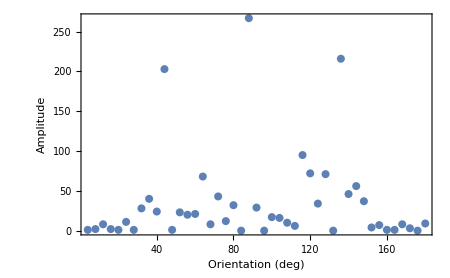
-Graphics-Orientation distribution

Lengths of p1s and p2s: {1554,1575}

Error weighted vector summation, Final : 12.5869

Moment of Inertia Algorithm

Moment of Inertia one pass with iteration factor = 3 and image size {rows, columns}={100,100} took 0.375 (s)

Moment of Inertia one pass with iteration factor = 5 and image size {rows, columns}={100,100} took 0.297 (s)

Moment of Inertia one pass with iteration factor = 7 and image size {rows, columns}={100,100} took 0.437 (s)

Moment of Inertia one pass with iteration factor = 9 and image size {rows, columns}={100,100} took 0.563 (s)

Moment of Inertia one pass with iteration factor = 11 and image size {rows, columns}={100,100} took 0.656 (s)

Moment of Inertia one pass with iteration factor = 17 and image size {rows, columns}={100,100} took 1.141 (s)

-Graphics-

Lengths of p1s and p2s: {1554,1575}

Error Moment of Inertia, one of the ROIs : 24.3089

Lengths of p1s and p2s: {1553,1575}

Error Moment of Inertia, one of the ROIs : 11.1037

Lengths of p1s and p2s: {1554,1575}

Error Moment of Inertia, one of the ROIs : 15.305

Lengths of p1s and p2s: {1552,1575}

Error Moment of Inertia, one of the ROIs : 11.1753

Lengths of p1s and p2s: {1554,1575}

Error Moment of Inertia, one of the ROIs : 12.3449

Lengths of p1s and p2s: {1543,1575}

Error Moment of Inertia, one of the ROIs : 11.5749

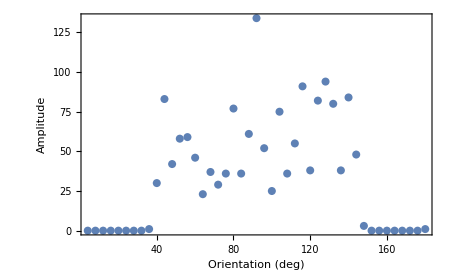
-Graphics-Orientation distribution

Lengths of p1s and p2s: {1554,1575}

Error Moment of Inertia, overall : 18.5045

Fourier Transformation Algorithm

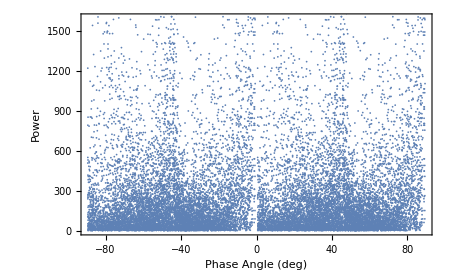
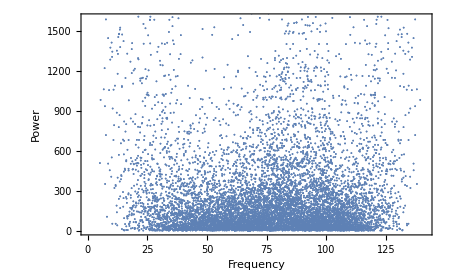
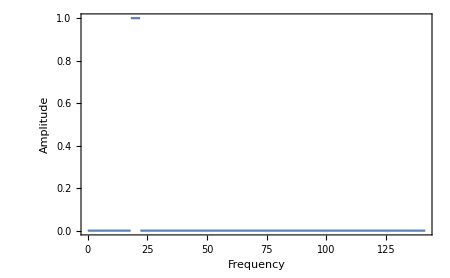
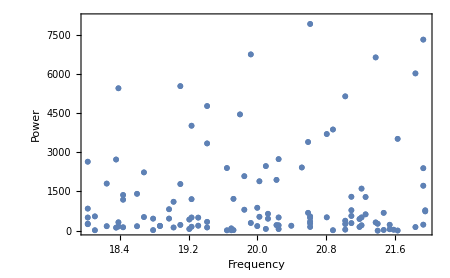
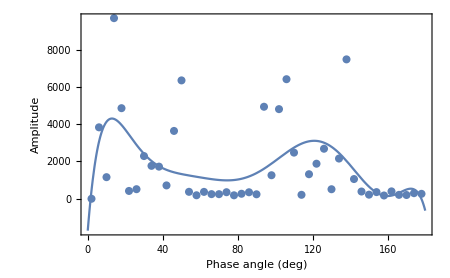
-Graphics-Original image-Graphics-Magnitude spectrum-Graphics-Phase spectrum-Graphics-Phase Angle vs. Power-Graphics-Radial Frequency vs. Power-Graphics-Bandpass Filter-Graphics-Bandpass Filtered - Radial Frequency vs Power-Graphics-Angular Amplitude Plot-Graphics-Reconstructed image

Lengths of p1s and p2s: {1572,1575}

Error Fourier Analysis Method : 15.7888

Gradient Filter Algorithm

-Graphics-

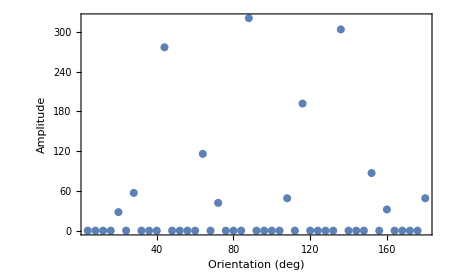
-Graphics-Orientation distribution

Lengths of p1s and p2s: {1554,1575}

Error Graphic Orientation Filter Method : 11.5367

Time taken for Vector Summation: 4.641 (s)

Time taken for Moment of Inertia: 5.063 (s)

Time taken for Fourier Analysis: 2.156 (s)

Time taken for Gradient Filter: 1.406 (s)

Total time consumed was: 13.329 (s)

```mathematica
initialize[];
perform[];
```

```mathematica
(** Post processing : Viewing Vector plots after algorithm has been run **)
ins=Graphics@Inset[img,{0,0},{-0.5,-0.5}, img//ImageDimensions];
lvps=ListVectorPlot[#//Reverse//Transpose,PlotTheme->"Scientific",VectorScale->Small, VectorPoints->70] &/@ {ivf1, ivf3};(* {vfs1[[1]],vfs1[[2]],vfs1[[3]],vfs1[[4]], vfs2[[1]], vfs2[[2]], vfs2[[3]], vfs2[[4]],ivf1,vf2,vf3,ivf3,vf}*);
graphics =Show[{ins, Graphics@#},ImageSize->Large,Axes->True, PlotRange->{{0,100},{0,100}}]&/@lvps;
Print@graphics;
```